## Cloud Functions & Deployment

#### CloudObject

```mathematica
CloudObject[]
```

CloudObject[https://www.wolframcloud.com/obj/2c41e3d4-9db0-4631-b160-c74929a31aa4]

```mathematica
CloudObject["/daily-summary.nb"]
```

CloudObject[https://www.wolframcloud.com/obj/burbery1/daily-summary.nb]

```mathematica
CloudObject["daily-summary.nb"]
```

CloudObject[https://www.wolframcloud.com/obj/burbery1/daily-summary.nb]

```mathematica
CloudObject["daily.nb","reports/summaries"]
```

CloudObject[https://www.wolframcloud.com/obj/burbery1/reports/summaries/daily.nb]

```mathematica
CloudObject["user:example-user@wolfram.com/file"]
```

CloudObject[https://www.wolframcloud.com/obj/examples/file]

```mathematica
CloudObject["mydir/myfile"]
```

CloudObject[https://www.wolframcloud.com/obj/burbery1/mydir/myfile]

```mathematica
CloudPut[2^128,CloudObject["answer"]]
```

CloudObject[https://www.wolframcloud.com/obj/burbery1/answer]

```mathematica
CloudGet[CloudObject["answer"]]
```

340282366920938463463374607431768211456

```mathematica
DeleteObject[CloudObject["answer"]]
```

```mathematica
directory=CreateDirectory[CloudObject[]]
```

CloudObject[https://www.wolframcloud.com/obj/2441e7b0-539b-4297-b8ea-e358d01e4727]

```mathematica
CloudDeploy[Notebook[{Cell["Weekly Summary","Title"],Cell["Monday","Section"],Cell["Tuesday","Section"],Cell["Wednesday","Section"],Cell["Thursday","Section"],Cell[Friday,"Section"]}],FileNameJoin[{directory,"index.nb"}]]
```

CloudObject[https://www.wolframcloud.com/obj/2441e7b0-539b-4297-b8ea-e358d01e4727/index.nb]

### Reading and Writing Cloud Objects

#### CloudGet

```mathematica
CloudPut[AstroGraphics[]]
```

CloudObject[https://www.wolframcloud.com/obj/ab9d9380-72bf-4649-94be-7ddfb4c3dfdf]

```mathematica
CloudPut[AstroGraphics[],"astrographics"]
```

CloudObject[https://www.wolframcloud.com/obj/burbery1/astrographics]

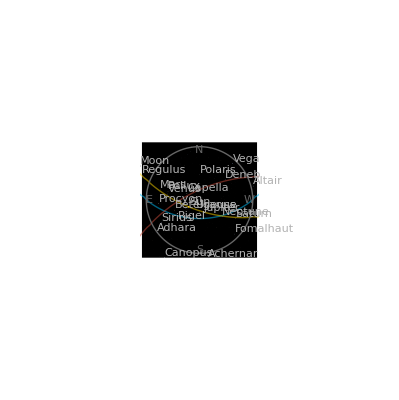

```mathematica
CloudGet["astrographics"]
```

```mathematica
CloudGet["https://www.wolframcloud.com/obj/burbery1/astrographics"]
```

-Graphics-

```mathematica
CloudGet[CloudObject["https://www.wolframcloud.com/obj/burbery1/astrographics"]]
```

-Graphics-

#### CloudPut

```mathematica
CloudPut[47!]
```

CloudObject[https://www.wolframcloud.com/obj/a121fc74-81de-4f42-a5dc-0a2b23931c34]

```mathematica
CloudGet[%]
```

258623241511168180642964355153611979969197632389120000000000

```mathematica
CloudPut[47!,"myfile"]
```

CloudObject[https://www.wolframcloud.com/obj/burbery1/myfile]

```mathematica
CloudGet["myfile"]
```

258623241511168180642964355153611979969197632389120000000000

#### CloudSave

```mathematica
f[x_]:=x!
```

```mathematica
obj=CloudSave[f]
```

CloudObject[https://www.wolframcloud.com/obj/bd890333-279f-4aff-94a2-52fe4efc2be3]

```mathematica
ClearAll[f]
```

```mathematica
f[2]
```

f[2]

```mathematica
CloudGet[obj]
```

```mathematica
f[2]
```

2

```mathematica
f[20]
```

2432902008176640000

```mathematica
ClearAll[f]
```

### Structured Data in the Cloud

#### CloudExpression

```mathematica
ce=CreateCloudExpression[{a,b,c}]
```

CloudExpression[…]

```mathematica
ce[2]
```

b

```mathematica
ce[2 ]=x
```

x

```mathematica
ce[]
```

{a,x,c}

```mathematica
AppendTo[ce,y]
```

CloudExpression[…]

```mathematica
ce[3]=.
```

```mathematica
ce[]
```

{a,x,y}

```mathematica
ce=CreateCloudExpression[<|"a"->1,"b"->1,"x"->1|>]
```

CloudExpression[…]

```mathematica
ce["b"]=2
```

2

```mathematica
AssociateTo[ce,"c"->3]
```

CloudExpression[…]

```mathematica
ce["x"]=.
```

```mathematica
ce[]
```

<|a→1,b→2,c→3|>

#### CloudSymbol

```mathematica
CloudSymbol["x"]=10!
```

3628800

```mathematica
CloudSymbol["x"]
```

3628800

### Cloud Evaluation

#### CloudEvaluate

```mathematica
CloudEvaluate[Table[If[MersennePrimeExponentQ[i],i,Nothing],{i,1000}]]
```

{2,3,5,7,13,17,19,31,61,89,107,127,521,607}

```mathematica
CloudEvaluate[{$OperatingSystem,$MachineID}]
```

{Unix,6500-45179-86363}

```mathematica
{$OperatingSystem,$MachineID}
```

{Windows,6240-49155-01989}

```mathematica
CloudEvaluate[Fibonacci[100],ff]
```

ff[354224848179261915075]

#### CloudFunction

```mathematica
CloudFunction[#1!+#2!&][3,4]
```

30

```mathematica
func=CloudPut[FactorInteger[#]&]
```

CloudObject[https://www.wolframcloud.com/obj/4fc5c166-49c4-4cd7-90f5-48f431a77c50]

```mathematica
CloudFunction[func][42]
```

{{2,1},{3,1},{7,1}}

#### CloudSubmit

```mathematica
CloudSubmit[{$MachineName,HandlerFunctions-><|"TaskFinished"->MessageDialog|>,HandlerFunctionsKeys->{"EvaluationResult"}}]
```

TaskObject[<|TaskUUID -> aea4a3d6-bc31-4d95-998d-fb84b03ae5f6, TaskEnvironment -> Cloud, TaskType -> Cloud, EvaluationExpression :> {$MachineName, <<2>>}, <<3>>, HandlerFunctionsKeys -> {TaskUUID, Task, TaskType, EvaluationExpression, EventName, TaskStatus, PrintOutput, MessageOutput, Failure, EvaluationResult, RemoteObject, RemoteDataObject}, AutoRemove -> True|>]

```mathematica
CloudSubmit[DateObject[],HandlerFunctions-><|"TaskFinished"->MessageDialog|>,HandlerFunctionsKeys->{"EvaluationResult"}]
```

TaskObject[<|TaskUUID -> 10abfb8c-c433-428d-998e-65c5ab393d3b, TaskEnvironment -> Cloud, TaskType -> Cloud, EvaluationExpression :> DateObject[], RemoteObject -> CloudObject[https://www.wolframcloud.com/obj/0901f1b6-cb93-4e04-a5f1-f17827c8093e], RemoteDataObject -> CloudObject[ht<<64>>753], HandlerFunctions -> <||>, HandlerFunctionsKeys -> {EvaluationResult}, AutoRemove -> True|>]

```mathematica
CloudSubmit[SendMail[StringTemplate["The ten millionth digit of pi is ``"][Last@First@RealDigits@N[Pi,1+10^7]]]]
```

TaskObject[<|TaskUUID -> 84a2cf25-e64f-41e0-b964-558f6f0304e1, TaskEnvironment -> Cloud, TaskType -> Cloud, EvaluationExpression :> SendMail[<<13>>e[<<34>>`][<<1>>]], <<3>>, HandlerFunctionsKeys -> {TaskUUID, Task, TaskType, EvaluationExpression, EventName, TaskStatus, PrintOutput, MessageOutput, Failure, EvaluationResult, RemoteObject, RemoteDataObject}, AutoRemove -> True|>]

```mathematica
CloudSubmit[Print["hello"],HandlerFunctions-><|"PrintOutputGenerated"->(MessageDialog[#PrintOutput]&)|>,HandlerFunctionsKeys->{"TaskUUID","PrintOutput","EvaluationResult"}]
```

TaskObject[<|TaskUUID -> e0c400d4-3164-4721-845f-ce9a39b8da55, TaskEnvironment -> Cloud, TaskType -> Cloud, EvaluationExpression :> Print[hello], RemoteObject -> CloudObject[https://www.wolframcloud.com/obj/0faa2531-8d0d-4367-8f42-7a0d8d475879], <<1>>, HandlerFunctions -> <||>, HandlerFunctionsKeys -> {TaskUUID, PrintOutput, EvaluationResult}, AutoRemove -> True|>]

```mathematica
CloudSubmit[1/0,HandlerFunctions-><|"MessageGenerated"->Print|>,HandlerFunctionsKeys->{"MessageOutput"}]
```

1
TaskObject[<|TaskUUID -> ca917d5d-4a05-46f2-a210-f7711608a9be, TaskEnvironment -> Cloud, TaskType -> Cloud, EvaluationExpression :> -, RemoteObject -> CloudObject[https://www.wolframcloud.com/obj/b79c5afe-6bab-4c64-94a7-3d8aa91ba087], RemoteDataObject -> CloudObject[https://www.<<51>>92d879], HandlerFunctions -> <||>, HandlerFunctionsKeys -> {MessageOutput}, AutoRemove -> True|>]
                                                                                                                                    0

```mathematica
CloudSubmit[1/0,HandlerFunctions-><|"MessageGenerated"->(Message[#MessageOutput]&)|>,HandlerFunctionsKeys->{"MessageOutput"}]
```

1
TaskObject[<|TaskUUID -> c2199938-770a-4434-bb4f-cf2433155239, TaskEnvironment -> Cloud, TaskType -> Cloud, EvaluationExpression :> -, RemoteObject -> CloudObject[https://www.wolframcloud.com/obj/a8645201-e734-4de6-bb01-953e56ecd2f8], RemoteDataObject -> CloudObject[https://www.<<51>>3005c0], HandlerFunctions -> <||>, HandlerFunctionsKeys -> {MessageOutput}, AutoRemove -> True|>]
                                                                                                                                    0

```mathematica
CloudSubmit[1+1,HandlerFunctions-><|"TaskStatusChanged"->Print|>,HandlerFunctionsKeys->{"TaskStatus"}]
```

TaskObject[<|TaskUUID -> 1c9d144a-f5db-4372-a4e4-b31d533fd1c4, TaskEnvironment -> Cloud, TaskType -> Cloud, EvaluationExpression :> 1 + 1, RemoteObject -> CloudObject[https://www.wolframcloud.com/obj/efb16829-22b0-4532-8ce5-82adb3094416], RemoteDataObject -> CloudObject[https://www<<51>>ccc176e], HandlerFunctions -> <||>, HandlerFunctionsKeys -> {TaskStatus}, AutoRemove -> True|>]

```mathematica
CloudSubmit[ScheduledTask[SendMail["Task executed on "<>DateString[]],{"Hourly",3}]]
```

TaskObject[<|TaskUUID -> 57c85686-5066-4270-a8ee-8faea5f233b1, TaskEnvironment -> Cloud, TaskType -> Cloud, EvaluationExpression :> ScheduledTask[<<2>>], <<3>>, HandlerFunctionsKeys -> {TaskUUID, Task, TaskType, EvaluationExpression, EventName, TaskStatus, PrintOutput, MessageOutput, Failure, EvaluationResult, RemoteObject, RemoteDataObject}, AutoRemove -> True|>]

```mathematica
tsObj=CloudPut[Now,"my-time-stamp"];
```

```mathematica
start=CloudGet[tsObj]
```

Sat 27 May 2023 11:17:58GMT-4

```mathematica
CloudSubmit[Pause[5];CloudPut[Now,"my-timestamp"]]
```

TaskObject[<|TaskUUID -> ebe8e9f7-152c-465b-b92a-b82035fed0c6, TaskEnvironment -> Cloud, TaskType -> Cloud, EvaluationExpression :> (Pause[5]; CloudPut[Now, my<<9>>p]), <<3>>, HandlerFunctionsKeys -> {TaskUUID, Task, TaskType, EvaluationExpression, EventName, TaskStatus, PrintOutput, MessageOutput, Failure, EvaluationResult, RemoteObject, RemoteDataObject}, AutoRemove -> True|>]

```mathematica
now=CloudGet["my-timestamp"]
```

Sat 27 May 2023 11:18:29GMT-4

```mathematica
QuantityMagnitude[now-start]>0
```

True

```mathematica
DeleteFile[CloudObject["my-timestamp"]]
```

### Cloud Deployment

#### CloudDeploy

```mathematica
CloudDeploy[Manipulate[Plot[Sin[x(1+a x)],{x,0,6}],{a,0,2}]]
```

CloudObject[https://www.wolframcloud.com/obj/8c630e6d-e875-4f07-b14a-81c39785d98d]

```mathematica
CloudDeploy[APIFunction[{},DateList[]&]]
```

CloudObject[https://www.wolframcloud.com/obj/340f3a62-4258-45c8-ab87-3fb0e5f15859]

```mathematica
CloudDeploy[FormFunction[{"x"->"Integer"},#x!&],"myform"]
```

CloudObject[https://www.wolframcloud.com/obj/burbery1/myform]

#### CloudPublish

```mathematica
publicObj=CloudPublish[Manipulate[Plot[Sin[x(1+a x)],{x,0,6}],{a,0,2}]]
```

CloudObject[https://www.wolframcloud.com/obj/24b20f61-478e-4dbe-991b-a1d6cc51bcaf]

```mathematica
Options[publicObj,{Permissions,AutoCopy}]
```

{Permissions→{All→{Read,Interact},Owner→{Read,Write,Execute}},AutoCopy→True}

```mathematica
CloudPublish[Manipulate[Plot[Sin[x(1+a x)],{x,0,6}],{a,0,2}],"SineExample"]
```

CloudObject[https://www.wolframcloud.com/obj/burbery1/SineExample]

```mathematica
obj=CloudDeploy[MatrixPlot[ExampleData[{"Matrix","FIDAP007"}]],"MatrixPlot",Permissions->"Private"]
```

CloudObject[https://www.wolframcloud.com/obj/burbery1/MatrixPlot]

```mathematica
published=CloudPublish[obj,"Published/FinalPlot"]
```

CloudObject[https://www.wolframcloud.com/obj/burbery1/Published/FinalPlot]

```mathematica
Options[published,Permissions]
```

{Permissions→{All→{Read,Interact},Owner→{Read,Write,Execute}}}

```mathematica
Options[obj,Permissions]
```

{Permissions→{Owner→{Read,Write,Execute}}}

So CloudDeploy is for private things and CloudPublish is for public things.

#### APIFunction

```mathematica
func=APIFunction[{"y"->"Number"->4},#y+3&][<||>]
```

7

```mathematica
func=APIFunction[{"x"->"Integer"},FactorInteger[#x]&]
```

APIFunction[{x→Integer},FactorInteger[#x]&]

```mathematica
api=CloudDeploy[func]
```

CloudObject[https://www.wolframcloud.com/obj/4209544b-1fee-485d-9c34-808f88bb5588]

```mathematica
APIFunction["x"->"Integer",Identity][<||>]
```

Failure[…]

```mathematica
APIFunction["x"->"Integer",Identity][<|"x"->3|>]
```

<|x→3|>

#### FormFunction

```mathematica
form=FormFunction[{"first"->"String","second"->"Number"},ff]
```

FormFunction[]

```mathematica
form[]
```

ff[<|first→lion,second→8|>]

```mathematica
CloudDeploy[form]
```

CloudObject[https://www.wolframcloud.com/obj/8eed05d8-5683-43a6-b09f-61bee9a791a5]

```mathematica
form[{"first"->"str","second"->"55"}]
```

ff[<|first→str,second→55|>]

```mathematica
form[{"first"->"str"}]
```

FormFunction[]

```mathematica
FormFunction[{"x"->"Boolean","y"->TemplateIf[TemplateSlot["x"],"Number","String"]},foo]
```

FormFunction[]

#### FormPage

```mathematica
CloudDeploy[FormPage["country"->"Country",GeoGraphics[#country]&]]
```

CloudObject[https://www.wolframcloud.com/obj/3c7a9d4b-b34f-4192-9e7c-f33edb45e2a8]

#### AskFunction

```mathematica
ask=AskFunction[Ask["x"->"Number"]+Ask["y"->"Number"]];
```

```mathematica
ask[]
```

9

```mathematica
CloudDeploy[ask]
```

CloudObject[https://www.wolframcloud.com/obj/c9f71664-bd72-4dc9-9ec5-dee598914644]

```mathematica
ask2=ask[<|"x"->3|>]
```

AskFunction[<|x→<|Value→3|>|>,Ask[x→Number]+Ask[y→Number]]

```mathematica
ask2[]
```

58

#### ExternalBundle

```mathematica
bundle=CloudDeploy[ExternalBundle[{"compress"->APIFunction[{"text"},Compress[#text]&,"Text"],"uncompress"->APIFunction[{"text"},Uncompress[#text]&,"Text"]}]]
```

CloudObject[https://www.wolframcloud.com/obj/1392677a-7d42-41d9-ad1e-e7d7a1d7ba27]

```mathematica
uncompress=FileNameJoin[{bundle,"uncompress"}]
```

CloudObject[https://www.wolframcloud.com/obj/1392677a-7d42-41d9-ad1e-e7d7a1d7ba27/uncompress]

```mathematica
StringTake[URLExecute[uncompress,<|"text"->Compress[ExampleData[{"Text","DeclarationOfIndependence"}]]|>],400]
```

When in the Course of human events, it becomes necessary for one people to dissolve the political bands which have connected them with another, and to assume, among the Powers of the earth, the separate and equal station to which the Laws of Nature and of Nature's God entitle them, a decent respect to the opinions of mankind requires that they should declare the causes which impel them to the sepa

```mathematica
StringTake[URLExecute[uncompress,<|"text"->"1:eJx9Wdty3DYSzadw92H3ZeIPiJ5kJbbiyLZK0paeMSRmCIsEGIDQaPzF+xl7TjdAcuLUVrmsmSHZ6Mvp7tPNf+zDw+N///nTT8+99Y3zzdzb5ibkmGwTDk2fR+Mb+2r9nHaNm5u9bcNoU+Nta1My8dwcQmyCt81kwzTYZg5N51IKw6sVWVMY3OxaMzR747vUnHrX9k1vcLkNHmJm2/HGsTm5uW+MD/gSd/jQUZZJKY8WX8fgjyLwPpxsTFSO36yJc7+Tj8lOJprZyqP2z4wj02xmFzwF6bm8786c5PEvZs5R716+/Ts1HwOe9rObBzFgxNlNB2v93ESbJihMcRQUJuchXYTBTS8OkiIOdrgPN5iZd52b1Ic8dJQxmKhOaU1OtvrCjZMd1AVFcLEEst81z7bpwyAuQkjmmOc+8b49bxsOP9tX10G3nR5ohqEZEUge1EZr6FxxxW6jEC9a38GPXbM/8zcXmxvejVBKFFobZwMwZG8GZ73ZwxcP7tgTBHpODQd0org7d0CQ7tweD55L8Bh84CgDNXDQrZngLmDm3c8/P4kqAQa0WT0CMbHI/xhebfQjESeinU8IRqYleupn63fwZnSvTnWA9t9ymgE1QcYhhlG9jNgwbAUqRxFsu11R4ATEA9kR2p6bDyGOvHE9fYF6ZxPc3s7u1RZRSfynCeGSCBfv1JPul1Qww4wD4FZ+3iMVEuI9L+hebEM+nTZn75rBnGmdgxMOIftOcYx/KQMyU3S+dTgjKXzj0Xj3vT5Q/ODKzUhQgjgVdI0AJGGSLD6OAX4b3IsdzrxsDwfBt/j00RzsfJYD1uA19zEDby2iDbhbeBOIgbTOtTNzT9CxDeHAkMGDwBCMRxBLOiDPieG2N/6IX1lFBvGhuCYanxyDoJlyJb+atg2xg5VQlhbYtwkooDKoJ0AtJJ98AWjNRyJoDPgPRWkKyYrbU4adqDHIP4QJGTQo1PR3ol2kSN0QWIrfkG6vcDgypkSywE8cnC5qjOYY9AUsgaHuXfM+K+BQTMQjsBDxAV7MXkoB7cspx0kCDWhp6jCi/tVEB6XOWhvMaJuv+2+MEzSH8UkKVHJH1dd2udXKhfTtCO89qjEx9ivKV5hdGjfARZzFwsufuswsFrzEcIKaB4XSFqEFwlMMrEAK4GxilySWKueQpcRKnrv5jNR/zFL94UZrtdnQYka6OJ/RXLLsJsBZrsZfVICOHirxSe1BkFscz3wXv6almmr+FWUQJnx5PKcZwbxM9nfNEwT2DuFCSytpPKGOU7M/GAbezhLZvIcljJ2j3zdPRDtpvXX+G6z9u5gStOh8GlUgMjKIQWMpzaymyVjKFiC4RO/pDOegUlHn4p5Hphxy8knDwKg7HDPYuflg2jlJk8j70c2zAt8gn3znuuYU4gBU3lqJRbSHzNTA0811EptxM/ukdlapEie0IZuAZrHrsv9rrYfqLapsWAXj2t51qBciWt0douTKhM6+tGI3Iklc7d30exInjVNAI5Jqkz1OTzAHLRiw7gpXQVwDqkBp86xEGyNKqYEXwp4xs50CSRIxhVXYrulV4QxPRWSat8ehUBN4DT8q2AmrH7xWjRHioiZVn7BijWOo1fuAsh6PUovm6Bgg/KS8aTFw7lGlKpk6if7RDs6DViTlL7G2mgdbEKriC3m7s0eXBmEzpC56N4v37EZp5LUN0BPMCdctPxNi1MoP58VMULdBrDxaMXAo8tkO96EToKP3DoaVKHsAnmwje1h+YPSkmvIsWg3xa3/uLCqy22QcgnmvKHqwLPWAX/UkkkDoBGs47z5AgWMuFXiEfVAfJ06DkwoiLIZIGK1BBjJJijmVnHYX7oMtt0EKcU3j4ayHh4lK4hwRibYCdBxcHNkN5QTW56Q00K/xWQiqRvIH0FB0bQVOCO6BlUpKnKqYS9GgYWyCiq/K/azC84pYjlZZ3BJ6mqM0mV26NZMEGApde+/Q8wQvOyXh0QIp3lZ4V+6CkCpW12Ju32xsXbJXcp/UHjw9Iq9KQZNSYdk2YRG7c+23rHsScPZ65e7Va4oG+jbk0lRQxl/zoC7lBecX7zFZzSumk5J2USaTMmdMeVjybFsfr4oNRGkF0L5QutLBL0YCUN7viyDwQovOCq2vNHbyyDbjJSIgIdDKHG3x1eiOpSb1bp1n0JtSPRJWdm6u4wO75/WEIg5mZ5Zf7zgxLcZXpXVeaq67EZ5nw6u6fgLbcKyVgMOi6481XdyxtBre8ymDvjkWc0XNcuRo0Nm/5e4oNFhqJRuTlvNnVlsDCNs1TVEo2fCXdAZzgEZpnQhA4bNXkjeZ87jSc9ycDCDnNrlqo9Zg04x5IFHuRPQXOOvrVrBYp45u0slE7e56i8anxzzFgOVYAK4Psp8Dd/X8vE/SbRYFXuxUZ50suSTQLmXb0NWAmCclba5RSG2qSC5j9DJ/8OBhLcyriUYYt8I5WuFrfPSzw9TMgJBkL34/FBpE2qszhRyDQWjQyK1FO4x79jutWitOYaKwjZyUDpCpJHJ3SUXFOq9QX6FTnE6kWAiZ8aZ9AftCPzjq7Ch2AVNXzVHHsUu4qV+va6dDrdHevfSQ4H9hijUYUSPqHyVo2SmdhSaDtXEiCGFKSyz0KeTLbJcsHgX4wEpoX5on5BHakFSX++wrp5KyCxL1OceOLtkw9kIW2LDdXGv57743ezdrV7wsK6pCC8ag9FCD/BSZMrrKQHpgjl9bgZAufYzMRkuBebPSOfKKHcop2NG7AYEy7RYUjrShNYkJUITvMcwenB4mxtMZn3I8qwiZqMimVApuP6MANY/W1I4CRlL60honWMXxqtj617EnWlvYNA/9DXMZKYqUGMdBxwNN/R7W8Il7zgnC5C5KD5FpebdHBsHTkaA//mXMsJ6gqOPte5mHhWGnUObakjoIHDOaDIBrqzczSi8j0eF4w/EgLzgAZ4gBw1K1RyarhW7HPFilFZejSHGneeFj5mQ0B256wS/r0eokXhDq/GqGLC1YKbXMskOB+4HGUCfARbv4h1AKGJ/fjNJ6cuGsVT4m3i3jK9J111TzogyuaLlwfa0JUi/oupqL2uqzxg7QFXghQcycAtcka8nao2DIpLNZljCMkn/r0TlJbeUWEUXhvuRq8ErBjcTz2QBWR45srEnLEdMgoysRCBsTQLpD83w1x/LLTTCJu6I9qIvmywxHLMYjzOFc2uTgXu3izQ0Zc0JbOTApXblIEK1BRks62WapjJgfW+sVe5VwWl2rMbtf5GZQFK4koUYohESan45vHAIxRnZnpNwx+7Juc7HNo/YeEXETsx0w1/4LGseDw92pNTgaCOFmEIR8WCYghdjeRPwDhYU7l34bFFTZQ7e5X+baW5wvlRUHo3W475Dly7px6R9llC4OP9hhwNR9A8by3XK+Ni8YoW7MpFsxVaRHum8qCkJ7TSTX+JY9I/t/1O2Cbth09H2zrXSadbfLkZ3rnU4n6feoSn3k7k9b36Gwys1eRh+6vWBN9q11xGrHXR7oEatAjlGhWBqKgE999jcscy9oLja6y4YgvonBz06SXxkwWLKMcr8jTVGGHgW4iesmck82UK/lBQLAVg6GqUM8cuHKKQnnZV2WLbtHZXg0WWUl+1Y2DCuRfIcTuatHBQWWjps9ytdJZ2pazIUyif+9neWxUvQfbMdbLkDV51EmQ4sw/tJ8ha3LkqM+nVSYbHOQQCdNWg5JQkK3KxGMlNcoA9oE1BcteVnLwUdWT5mMM74otVBDcLU06dGwuBwASQBXliGzeC171vbSw3ot3FHhLR3qvuT8Fxgpuj4XdU+QUCYXmfDrmwLGlEuemd1sX1D3bvEbIubrKwsdZaV8BP3LcyFsnOYNIjfMT4aFN9knSLghjZZId7ggY7LmYUms52LUctKU5eSSyj9UDipv1+lD2fE8D3ap0qtEMyE8wzL6QVGvs+M3HSTk6dEcvfEOnKjs9U92eXvzTVOE+pQJdHarGrL68A3XsCWTgG3k1amA8mI1pjHWfQdC/Opm2XiiAdsY8zRXRuqXxBXoR76SCV420rLD4xo7bDCJTD5UovwanC4Xt/bhK4udYcp57ijpnhE37JSbsPTD8PbPDNNaW/Nj2T1W1aECKptEAZo+Lm9wSlkpr3B0EX9a3+nwndK8eYG0A4+y0nZwELqj0L17zhrNBy2GVPBCN3n9cLHLWBjnf7zUPiWssgBAdULzFqkfwRjRS0g1j0z9nRB3Zjy0UGyUYVfm/YwTAPBPnAYvGO0y/ElRrUMavcDo+RLgLuyq776YscxfBTXXGcSXC+L1VU3o6ibih2XwTpZBI2uM7BxTv+E8EPxUXnSlxf76ZCPXS9TLG5ss632pHh9YLnj1983QVXcIl6/PrvdliSQVgGX5emCWy/KpeIw1hMrdRHktoRNweUe3vhVdMQ0V5lPZio/LwKx7lr9un0u/6C70r/1+WXFdbQ5N/8+8nVomaXPIw7Blh69nxSEUbQcG914nX3yfWbxpudidNtQeLh+FLC3vCTpdA+mSVCZCXngiUa5j2I96SdHnbl1i1QV0EL/iDYMwCZsiBP74VRBQsk5HMFnVyQJVXywoADdcFM/+ytHK6oBSXm2dWALmLN6cZNqVum3aMksLuu+YaTv5CGI+Z1/fxpGympY17zb4EOXlz4yzPp4cYj3PV83dma/VbyH/CmkYSDafMREEfyVbFWdGPMq99lXzCX1y6sFmTkThp9CzHHjc+FuH3tE1D3kWBa/gyzAizLf2zAu75lN8t/x4h9LUl5+uwQWh4mfXdYOVM0UqaFOLyfkKfGUE++RIw11f1efetGYR94jHcI1TD99B3qCJBQb3UD+K2GrZGS67Qr6x28Mn1qOv39lV40987RgTH3lv/TeDPgdtIpohfyo3fbFDYlzFhA98T4SI3xEXhxBmlXcjQxhyxLyJAg+B76Obz4GyNsIfcuo3XyntBbWuOAK3b9W/Gc6jBMJw8/OIRtgv157MeQjLNbgqbR58CClRJ5vAhB9C5+15vQYKvpj2uf3Dmk3oPwzhjKv3Pbj5RJgxR0SlxW57okHyZzGvOhjBaV/WuD7LXgxdcivgNkzoNmkT/AhYXu+j6aHADdLoRaDnTN+8x7VBYFsVfO7dhLRYoHKNCbaCs3wurn+SonXPQQKIHUClmUsf0dPhi8cZyEa9K8qs8n9DLeUND+HIF3ZQf6R/ymm3WXjbRbaUv5DxlQNfbJ7D0Abq/Bl0rLcn+hqzYvD/Ayanq7o="|>],400]
```

When in the Course of human events, it becomes necessary for one people to dissolve the political bands which have connected them with another, and to assume, among the Powers of the earth, the separate and equal station to which the Laws of Nature and of Nature's God entitle them, a decent respect to the opinions of mankind requires that they should declare the causes which impel them to the sepa

#### URLDispatcher

```mathematica
CloudDeploy[URLDispatcher[{"/api"->APIFunction["x"->"String"],"/form"->FormFunction["x"->"String"]}],"application"]
```

CloudObject[https://www.wolframcloud.com/obj/burbery1/application]

```mathematica
co=CloudDeploy[URLDispatcher[{"/"~~base:Repeated[DigitCharacter,3]~~"^"~~power:Repeated[DigitCharacter,3]:>ExportForm[FromDigits[base]^FromDigits[power],"WL"]}]]
```

CloudObject[https://www.wolframcloud.com/obj/053bc71c-03dc-4b2e-8af6-fb691c4e7b10]

```mathematica
URLRead[CloudObject[First[co]<>"/12^56"],"Body"]
```

2717376270889601918875979639080849756517127883888251440726016

```mathematica
URLRead[CloudObject[First[co]<>"/3^3"],"Body"]
```

27

```mathematica
CloudObject[First[co]<>"/3^3"]
```

CloudObject[https://www.wolframcloud.com/obj/053bc71c-03dc-4b2e-8af6-fb691c4e7b10/3^3]

### Deployment Features

#### ExportForm

```mathematica
CloudDeploy[ExportForm[Graphics[Style[Disk[]]],"GIF"]]
```

CloudObject[https://www.wolframcloud.com/obj/c39b8bb1-4111-4f54-b3af-bb311d738e9e]

```mathematica
CloudImport[%]
```

-Graphics-

```mathematica
CloudDeploy[ExportForm[Graphics[Disk[]],"Text"]]
```

CloudObject[https://www.wolframcloud.com/obj/2e6d3b1e-62cf-4540-9d94-5486a550f8f1]

```mathematica
CloudImport[%]
```

Graphics[Disk[{0, 0}]]

```mathematica
CloudDeploy[ExportForm[{"one"->1,"two"->2,"three"->3},"JSON"]]
```

CloudObject[https://www.wolframcloud.com/obj/e70f6f06-b983-4307-a0f2-187419f107a3]

```mathematica
CloudImport[%,"JSON"]
```

{one→1,two→2,three→3}

#### Delayed

```mathematica
obj=CloudDeploy[Delayed[DateString[]]]
```

CloudObject[https://www.wolframcloud.com/obj/627bd676-6d34-4c8a-a06f-f34988a07652]

```mathematica
Hyperlink[First[obj]]
```

https://www.wolframcloud.com/obj/627bd676-6d34-4c8a-a06f-f34988a07652

#### AutoRefreshed

```mathematica
o=CloudDeploy[AutoRefreshed[Now]]
```

CloudObject[https://www.wolframcloud.com/obj/84712b27-b8df-4c40-bf48-643dfe655ae8]

```mathematica
TaskRemove[o]
```

CloudObject[https://www.wolframcloud.com/obj/84712b27-b8df-4c40-bf48-643dfe655ae8]

```mathematica
o=CloudDeploy[AutoRefreshed[MoonPhase["Icon"],"Daily","PNG"]]
```

CloudObject[https://www.wolframcloud.com/obj/3cdaf31e-d1e9-4f5f-a73f-ff47c6bfddcb]

```mathematica
TaskRemove[o]
```

CloudObject[https://www.wolframcloud.com/obj/3cdaf31e-d1e9-4f5f-a73f-ff47c6bfddcb]

#### ScheduledTask

```mathematica
obj=SessionSubmit[ScheduledTask[Print[DateString[]],{Quantity[1,"Seconds"],3}]]
```

TaskObject[<|TaskUUID -> e7f2f8b2-e80e-4a82-babe-5314c831e21d, TaskEnvironment -> Session, TaskType -> Scheduled, <<3>>, HandlerFunctionsKeys -> {Task, TaskUUID, TaskType, TaskStatus, TaskEnvironment, HandlerFunctions, HandlerFunctionsKeys, EventName, EvaluationExpression, <<4>>, Re<<12>>unt, NextScheduledTime, TotalRunCount, MessageOutput, PrintOutput}, AutoRemove -> True|>]

```mathematica
obj=CloudDeploy[ScheduledTask[{Now,AirTemperatureData[]},"Hourly"]]
```

CloudObject[https://www.wolframcloud.com/obj/f64459ab-0a30-4ad0-8f59-6685483eb0ab]

```mathematica
TaskRemove[obj]
```

CloudObject[https://www.wolframcloud.com/obj/f64459ab-0a30-4ad0-8f59-6685483eb0ab]

```mathematica
obj=LocalSubmit[ScheduledTask[DateString[],{Quantity[1,"Seconds"],3}],HandlerFunctions-><|"ResultReceived"->Print|>,HandlerFunctionsKeys->"EvaluationResult"]
```

StringForm::sfr: Item 2 requested in "Value `1` returned from `2` was not an integer." out of range; 1 items available.

Internal`CreateAsynchronousTask::id: Value $Failed returned from `2` was not an integer.

LinkObject::linkn: Argument LinkObject["C:\Program Files\Wolfram Research\Wolfram Desktop\13.2\WolframKernel" -noinit,32973,41] in LinkClose[LinkObject["C:\Program Files\Wolfram Research\Wolfram Desktop\13.2\WolframKernel" -noinit,32973,41]] has an invalid LinkObject number; the link may be closed.

LocalSubmit::tasknc: Could not create the task.

$Failed

```mathematica
TaskRemove[obj]
```

TaskRemove::timnf: The task 74a5799c-00b2-4505-bc29-5fa9ed0a6ee0 cannot be found.

$Failed

```mathematica
obj=LocalSubmit[ScheduledTask[DateString[],{Quantity[1,"Seconds"],3}],
HandlerFunctions-><|"ResultReceived"->Print|>,
HandlerFunctionsKeys->"EvaluationResult"
]
```

TaskObject[<|TaskUUID -> e32caa15-95f7-4237-8058-7e88a5981a77, TaskEnvironment -> Local, TaskType -> Scheduled, EvaluationExpression :> DateString[], HandlerFunctions -> <|ResultReceived -> Print|>, HandlerFunctionsKeys -> {EvaluationResult}, AutoRemove -> True|>]

```mathematica
TaskRemove[obj]
```

TaskObject[<|TaskUUID -> e32caa15-95f7-4237-8058-7e88a5981a77, TaskEnvironment -> Local, TaskType -> Scheduled, EvaluationExpression :> DateString[], HandlerFunctions -> <|ResultReceived -> Print|>, HandlerFunctionsKeys -> {EvaluationResult}, AutoRemove -> True|>]

```mathematica
Needs["Wolfram`CodeEquivalenceUtilities`"]
```

```mathematica
CodeEquivalentQ[obj=LocalSubmit[ScheduledTask[DateString[],{Quantity[1,"Seconds"],3}],
HandlerFunctions-><|"ResultReceived"->Print|>,
HandlerFunctionsKeys->"EvaluationResult"
](*my input*),obj=LocalSubmit[ScheduledTask[DateString[],{Quantity[1,"Seconds"],3}],
HandlerFunctions-><|"ResultReceived"->Print|>,
HandlerFunctionsKeys->"EvaluationResult"
](*documentation input*)]
```

True

```mathematica
obj=CloudSubmit[ScheduledTask[SendMail[<|"To"->$WolframID,"Subject"->DateString[],"Body"->AirTemperatureData[]|>],{"Daily",DatePlus[DateObject["now"],Quantity[1, "Months"]]}]]
```

TaskObject[<|TaskUUID -> 569e2730-713e-40a3-8be4-a7b772e23a34, TaskEnvironment -> Cloud, TaskType -> Cloud, EvaluationExpression :> ScheduledTask[<<2>>], <<3>>, HandlerFunctionsKeys -> {TaskUUID, Task, TaskType, EvaluationExpression, EventName, TaskStatus, PrintOutput, MessageOutput, Failure, EvaluationResult, RemoteObject, RemoteDataObject}, AutoRemove -> True|>]

```mathematica
TaskRemove[obj]
```

TaskObject[<|TaskUUID -> 569e2730-713e-40a3-8be4-a7b772e23a34, TaskEnvironment -> Cloud, TaskType -> Cloud, EvaluationExpression :> ScheduledTask[<<2>>], <<3>>, HandlerFunctionsKeys -> {TaskUUID, Task, TaskType, EvaluationExpression, EventName, TaskStatus, PrintOutput, MessageOutput, Failure, EvaluationResult, RemoteObject, RemoteDataObject}, AutoRemove -> True|>]

```mathematica
obj=CloudDeploy[ScheduledTask[{Now,FinancialData["QQQ","Open"]},"* 10 * * 1,2,3,4,5"]]
```

CloudObject[https://www.wolframcloud.com/obj/1fe7b4fb-ef3d-4e97-8da4-f189eb1a337e]

```mathematica
TaskRemove[obj]
```

CloudObject[https://www.wolframcloud.com/obj/1fe7b4fb-ef3d-4e97-8da4-f189eb1a337e]

```mathematica
time=DateList[];
```

```mathematica
var=CloudSave[time];
```

```mathematica
obj=With[{co=var},CloudSubmit[ScheduledTask[time=DateList[];CloudSave[time,co],"Daily"]]]
```

TaskObject[<|TaskUUID -> d73ed1fd-e72b-4cda-82eb-dfa188accd4c, TaskEnvironment -> Cloud, TaskType -> Cloud, EvaluationExpression :> ScheduledTask[<<2>>], <<3>>, HandlerFunctionsKeys -> {TaskUUID, Task, TaskType, EvaluationExpression, EventName, TaskStatus, PrintOutput, MessageOutput, Failure, EvaluationResult, RemoteObject, RemoteDataObject}, AutoRemove -> True|>]

```mathematica
CloudGet[var]
```

{2023,5,27,13,26,44.5286496}

```mathematica
TaskExecute[obj]
```

TaskObject[<|TaskUUID -> d73ed1fd-e72b-4cda-82eb-dfa188accd4c, TaskEnvironment -> Cloud, TaskType -> Cloud, EvaluationExpression :> ScheduledTask[<<2>>], <<3>>, HandlerFunctionsKeys -> {TaskUUID, Task, TaskType, EvaluationExpression, EventName, TaskStatus, PrintOutput, MessageOutput, Failure, EvaluationResult, RemoteObject, RemoteDataObject}, AutoRemove -> True|>]

```mathematica
CloudGet[var]
```

{2023,5,27,13,26,44.5286496}

```mathematica
TaskRemove[obj]
```

TaskObject[<|TaskUUID -> d73ed1fd-e72b-4cda-82eb-dfa188accd4c, TaskEnvironment -> Cloud, TaskType -> Cloud, EvaluationExpression :> ScheduledTask[<<2>>], <<3>>, HandlerFunctionsKeys -> {TaskUUID, Task, TaskType, EvaluationExpression, EventName, TaskStatus, PrintOutput, MessageOutput, Failure, EvaluationResult, RemoteObject, RemoteDataObject}, AutoRemove -> True|>]

#### ContinuousTask

```mathematica
o=CloudDeploy[ContinuousTask[Pause[10];Now,NotificationFunction->All]]
```

ContinuousTask::restr: Unrestricted cloud required for deployment.

$Failed

```mathematica
TaskRemove[o]
```

TaskRemove::taskid: A string or a TaskObject is expected instead of $Failed.

TaskRemove[$Failed]

#### MailReceiverFunction

```mathematica
MailReceiverFunction[#From&][File["ExampleData/in.mbox"]]
```

"John Doe" <johndoe@docex.wolfram.com>

```mathematica
CloudDeploy[MailReceiverFunction[SendMail[#From<>" sent your receiver mail about "<>#Subject]&]]
```

CloudObject[mailto:[receiver+1dJfHHgo2@wolframcloud.com](mailto:receiver+1dJfHHgo2@wolframcloud.com)]

```mathematica
CloudDeploy[MailReceiverFunction[CloudPut[#Body,"MailLog"]&]]
```

CloudObject[mailto:[receiver+1dJfJnPR7@wolframcloud.com](mailto:receiver+1dJfJnPR7@wolframcloud.com)]

```mathematica
SendMail[<|"To"->"receiver+1dJfHHgo2@wolframcloud.com","Body"->"Hello There"|>];
```

SendMail::cloudrelay: SendMail has relayed your message through the Wolfram Cloud.  A local SMTP server has not been configured. These settings can be defined through Preferences > Internet & Mail > Mail Settings in the notebook front end.

#### ChannelReceiverFunction

```mathematica
f=ChannelReceiverFunction[{#Message,#MessageID}&]
```

ChannelReceiverFunction[{#Message,#MessageID}&]

```mathematica
f[<|"Message"->"message","MessageID"->"id"|>]
```

{message,id}

```mathematica
f=ChannelReceiverFunction[CloudPut[#Message,CloudObject["LastMessage"]]&]
```

ChannelReceiverFunction[CloudPut[#Message,CloudObject[LastMessageLastMessageNoneLastMessage]]&]

```mathematica
object=CloudDeploy[f]
```

CloudObject[https://www.wolframcloud.com/obj/e73b5c01-e84b-4a28-886f-d9a089a4f969,MetaInformation→{Channel→mqtts://channelbroker-mqtt.wolframcloud.com:8883/channels/fd1857d5-a609-45cf-a27a-6deca785ffdb}]

```mathematica
channel=ChannelObject[object]
```

ChannelObject[mqtts://channelbroker-mqtt.wolframcloud.com:8883/channels/fd1857d5-a609-45cf-a27a-6deca785ffdb]

```mathematica
ChannelSend[channel,"hello"]
```

```mathematica
CloudGet[CloudObject["LastMessage"]]
```

hello

```mathematica
DeleteChannel[channel];
DeleteObject[object];
```

```mathematica
bin=CreateDatabin[];
f=ChannelReceiverFunction[DatabinAdd[bin,#]&]
```

ChannelReceiverFunction[DatabinAdd[bin,#1]&]

```mathematica
object=CloudDeploy[f]
```

CloudObject[https://www.wolframcloud.com/obj/07bdfbd0-778a-41e4-a5f2-bded868c73ef,MetaInformation→{Channel→mqtts://channelbroker-mqtt.wolframcloud.com:8883/channels/2d996f53-850b-419c-9d44-1593dc1a1220}]

```mathematica
channel=ChannelObject[object]
```

ChannelObject[mqtts://channelbroker-mqtt.wolframcloud.com:8883/channels/2d996f53-850b-419c-9d44-1593dc1a1220]

```mathematica
ChannelSend[channel,"hello"]
```

```mathematica
bin["Entries"]
```

{<|RequesterWolframID→burbery1@marshall.edu,Message→hello,RequesterWolframUUID→d9feca95-da0d-4506-8a55-0cb34d332938,MessageID→34cd7a92-f2cb-4968-bdfa-5f652baa39b1|>}

```mathematica
bin["Timestamps"]
```

{Sat 27 May 2023 14:04:04GMT-4,Sat 27 May 2023 14:04:23GMT-4}

```mathematica
DeleteChannel[channel];
DeleteObject[{object,bin}];
```

### Creating Embeddable Content

#### EmbedCode

```mathematica
EmbedCode[CloudDeploy["hello, world"]]
```

Embeddable Code
Use the code below to call the Wolfram Cloud function from HTML:
Code
 | Copy to Clipboard
<iframe src="https://www.wolframcloud.com/obj/9423daca-d385-4249-9fa7-2816e9ea087b?_embed=iframe" width="600" height="800"></iframe>

```mathematica
EmbedCode[CloudDeploy["hello, world"],ImageSize->{200,200}]
```

Embeddable Code
Use the code below to call the Wolfram Cloud function from HTML:
Code
 | Copy to Clipboard
<iframe src="https://www.wolframcloud.com/obj/c6d8b307-ca8b-4144-881b-aefdabc78c2b?_embed=iframe" width="200" height="200"></iframe>

```mathematica
EmbedCode[APIFunction[{"x"->"Integer"},(#x)^2&],"Java"]
```

Embeddable Code
Use the code below to call the Wolfram Cloud function from Java:
Code
 | Copy to Clipboard
import java.net.URL;
import java.net.HttpURLConnection;
import java.net.URLEncoder;
import java.io.InputStream;
import java.io.BufferedReader;
import java.io.InputStreamReader;
import java.io.DataOutputStream;
import java.io.IOException;

public class WolframCloudCall {

    public static String call(int x) throws IOException {

        URL _url = new URL("https://www.wolframcloud.com/obj/b3d40915-b263-4245-995e-a5121d2186db");
        HttpURLConnection _conn = (HttpURLConnection) _url.openConnection();
        _conn.setRequestMethod("POST");
        _conn.setDoOutput(true);
        _conn.setDoInput(true);
        _conn.setUseCaches(false);
        _conn.setAllowUserInteraction(false);
        _conn.setRequestProperty("Content-Type", "application/x-www-form-urlencoded; charset=utf-8");
        _conn.setRequestProperty("User-Agent", "EmbedCode-Java/1.0");
        DataOutputStream _out = new DataOutputStream(_conn.getOutputStream());

        _out.writeBytes("x");
        _out.writeBytes("=");
        _out.writeBytes(URLEncoder.encode("" + x, "UTF-8"));
        _out.writeBytes("&");

        _out.close();

        if (_conn.getResponseCode() != 200) {
            throw new IOException(_conn.getResponseMessage());
        }
        
        BufferedReader _rdr = new BufferedReader(new InputStreamReader(_conn.getInputStream()));
        StringBuilder _sb = new StringBuilder();
        String _line;
        while ((_line = _rdr.readLine()) != null) {
            _sb.append(_line);
        }
        _rdr.close();
        _conn.disconnect();
        return _sb.toString();
    }
}

```mathematica
EmbedCode[APIFunction[{"i"->"Integer"},(#i)^2&],"Python"]
```

Embeddable Code
Use the files and code below to call the Wolfram Cloud function from Python:
Dependencies
  Install the [wolframclient](https://pypi.org/project/wolframclient) library.


Code
 | Copy to Clipboard
# -*- coding: utf-8 -*-

from __future__ import absolute_import, print_function, unicode_literals
from wolframclient.evaluation import WolframCloudSession

def call(i):
    """ Call the API using function input parameter values.
    If the API was deployed with an export formats set to JSON or WXF, the result is often a native Python type.
    """
    with WolframCloudSession() as session:
        api_response = session.call('https://www.wolframcloud.com/obj/aa5d5c1b-109c-4762-babf-ee1ef73e97ba', {'i' : i})
        return api_response.get()

### Detailed Control of Web Behavior

#### ResponseForm

```mathematica
CloudDeploy[APIFunction[{"x"->"String"},ResponseForm[#x,"JSON"]&]]
```

CloudObject[https://www.wolframcloud.com/obj/38703fd2-df21-44b4-be97-caf5e12937ec]

```mathematica
CloudDeploy[APIFunction[{"x"->"String"},ResponseForm[#x,"XML"]&]]
```

CloudObject[https://www.wolframcloud.com/obj/06273868-f395-4e5c-a10c-e16c5a6f2ff8]

```mathematica
CloudDeploy[APIFunction[{"m"->Number,"n"->Number},ResponseForm[Mod[#m,#n],None]&]]
```

CloudObject[https://www.wolframcloud.com/obj/7ff77c6c-064f-4d30-9025-e2859bb2a295]

```mathematica
api=CloudDeploy[APIFunction[{"x"->"Integer"},ResponseForm[Fibonacci[#x],"JSON"]&]]
```

CloudObject[https://www.wolframcloud.com/obj/07ebff8d-0c09-47b8-a4bd-643dbc51fa01]

```mathematica
URLExecute[api,{"x"->20},"JSON"]
```

{StatusCode→200,Success→True,FailureType→Null,OutputLog→{},Timing→0.015,AbsoluteTiming→0.015,Messages→{},MessagesText→{},MessagesExpressions→{},InputString→GenerateHTTPResponse[APIFunction[{"x" -> "Integer"}, ResponseForm[Fibonacci[#x], "JSON"] & ], <|"PathString" -> "/obj/07ebff8d-0c09-47b8-a4bd-643dbc51fa01", "Domain" -> "www.wolframcloud.com", "Scheme" -> "https", "Port" -> "443", "QueryString" -> "x=20", "Method" -> "GET", "Headers" -> {"host" -> "www.wolframcloud.com", "accept" -> "*/*", "accept-encoding" -> "deflate, gzip", "user-agent" -> "Wolfram HTTPClient 13.2", "x-forwarded-proto" -> "https", "x-forwarded-for" -> "76.26.77.249, 10.17.16.157", "x-custom-cookie-set-by-apache" -> "false", "x-forwarded-host" -> "www.wolframcloud.com", "x-forwarded-server" -> "www.wolframcloud.com"}, "Parameters" -> {"x" -> "20"}, "SessionID" -> "WgeFwMaWN5NNUiYuFBVYAJZYT4uNvLB0Co54L6ujWZ4", "MultipartElements" -> None, "DispatchedPathString" -> "/", "DispatchPathString" -> "/", "Body" -> "", "BodyByteArray" -> {}, "FormRules" -> {}|>],Result→6765,ResultMeta→{StatusCode→200,ContentType→text/plain;charset=utf-8,Headers→{content-type→text/plain;charset=utf-8}}}

```mathematica
CloudFunction[api][{"x"->20}]
```

ResponseForm[Fibonacci[20],JSON]

#### HTTPResponse

```mathematica
response=URLRead["https://www.wolfram.com"]
```

HTTPResponse[…]

```mathematica
response["StatusCode"]
```

200

```mathematica
response["Headers"]
```

{date→Sat, 27 May 2023 18:14:40 GMT,server→Apache,content-location→index.en.html,vary→negotiate,accept-language,tcn→choice,accept-ranges→bytes,keep-alive→timeout=2, max=100,connection→Keep-Alive,transfer-encoding→chunked,content-type→text/html,content-language→en}

```mathematica
response["ContentType"]
```

text/html

```mathematica
Snippet[response["Body"],6]
```

<!doctype html>
<html lang="en" class="homepage">
<head>

<!-- begin framework head en -->

```mathematica
response["BodyByteArray"]
```

ByteArray[…]

```mathematica
CloudDeploy@Delayed[HTTPResponse["Hello <strong>world</strong>"]]
```

CloudObject[https://www.wolframcloud.com/obj/7fa0e876-487e-40c4-8f3d-8251487cf794]

```mathematica
CloudDeploy@Delayed[HTTPResponse@TemplateApply[XMLTemplate["<h1><wolfram:slot id=1/></h1><wolfram: slot id=2/>"],{"Aerial",ExampleData[{"TestImage","Aerial"}]}]]
```

CloudObject[https://www.wolframcloud.com/obj/ae6349a9-a298-4e44-9d23-114e0e29de48]

```mathematica
SystemOpen[CloudObject["https://www.wolframcloud.com/obj/ae6349a9-a298-4e44-9d23-114e0e29de48"]⟦1⟧]
```

```mathematica
CodeEquivalentQ[CloudDeploy@Delayed[HTTPResponse@TemplateApply[XMLTemplate["<h1><wolfram:slot id=1/></h1><wolfram: slot id=2/>"],{"Aerial",ExampleData[{"TestImage","Aerial"}]}]](*my input*),CloudDeploy @ Delayed[
HTTPResponse @ TemplateApply[
XMLTemplate["<h1><wolfram:slot id=1/></h1><wolfram:slot id=2/>"], {"Aerial", ExampleData[{"TestImage","Aerial"}]}
]
](*documentation input*)]
```

True

```mathematica
CloudDeploy@Delayed[HTTPResponse[ExportString[ExampleData[{"TestImage","Aerial"}],"PNG"],<|"ContentType"->"image/png"|>]]
```

CloudObject[https://www.wolframcloud.com/obj/49004adc-b3f1-4078-95f5-0020c45db707]

```mathematica
CloudDeploy@FormFunction[{"example"->ExampleData["TestImage"][[All,2]]},HTTPResponse[ExportByteArray[ExampleData[{"TestImage",#example}],"PNG"],<|"ContentType"->"image/png","Headers"->{"content-disposition"->"attachment; filename=" <>#example <>".png"}|>]&]
```

CloudObject[https://www.wolframcloud.com/obj/212738c2-e855-4748-8c35-1da5a995ef4a]

This is helpful. You can use this to download images.

#### HTTPRedirect

```mathematica
CloudDeploy@Delayed[HTTPRedirect["http://www.wolfram.com/"]]
```

CloudObject[https://www.wolframcloud.com/obj/14bb7279-5b80-4d70-97dc-c0cf4eef4a24]

```mathematica
CloudDeploy@APIFunction["url"->"SemanticURL",Composition[HTTPRedirect,First]]
```

CloudObject[https://www.wolframcloud.com/obj/5907f7b7-91a9-4006-8e2e-f031dfd92165]

```mathematica
CloudDeploy@FormFunction["query"-><|"Hint"->"Search","Label"->None|>,HTTPRedirect[URLBuild["https://en.wikipedia.org/w/index.php",{"search"->#query}]]&]
```

CloudObject[https://www.wolframcloud.com/obj/d6b944f9-28ce-4c0e-bae8-c9efd1e225cd]

#### HTTPErrorResponse

```mathematica
GenerateHTTPResponse[HTTPErrorResponse[500]]
```

HTTPResponse[…]

```mathematica
CloudDeploy[Delayed@If[Now<=DateObject[{2024,1,1}],HTTPErrorResponse[404],"HelloWorld!"]]
```

CloudObject[https://www.wolframcloud.com/obj/27136185-2247-431b-af76-59256ad1b2db]

```mathematica
CloudDeploy[APIFunction["x"->"Number",If[0<=#x<=100,"Hello World",HTTPErrorResponse[404]]&]]
```

CloudObject[https://www.wolframcloud.com/obj/aeae99bd-aab0-43c6-98fd-12b936e359b3]

#### URLExecute

```mathematica
URLExecute["https://en.wikipedia.org/w/api.php",{"format"->"json","action"->"query","titles"->"Main Page","prop"->"revisions","rvprop"->"content"}]//Short
```

{batchcomplete→,…→«1»,query→{pages→{15580374→«1»}}}

```mathematica
URLExecute["https://placehold.it/400x200",{"text"->"Hello world"},"PNG"]
```

-Graphics-

```mathematica
deck=URLExecute["https://deckofcardsapi.com/api/deck/new/shuffle",{"deck_count"->1}]
```

{success→True,deck_id→seozj8hujmg9,remaining→52,shuffled→True}

```mathematica
cards=URLExecute["https://deckofcardsapi.com/api/deck/"<>Lookup[deck,"deck_id"]<>"/draw/",{"count"->4}]
```

{success→True,deck_id→seozj8hujmg9,cards→{{code→0D,image→https://deckofcardsapi.com/static/img/0D.png,images→{svg→https://deckofcardsapi.com/static/img/0D.svg,png→https://deckofcardsapi.com/static/img/0D.png},value→10,suit→DIAMONDS},{code→4C,image→https://deckofcardsapi.com/static/img/4C.png,images→{svg→https://deckofcardsapi.com/static/img/4C.svg,png→https://deckofcardsapi.com/static/img/4C.png},value→4,suit→CLUBS},{code→8H,image→https://deckofcardsapi.com/static/img/8H.png,images→{svg→https://deckofcardsapi.com/static/img/8H.svg,png→https://deckofcardsapi.com/static/img/8H.png},value→8,suit→HEARTS},{code→KD,image→https://deckofcardsapi.com/static/img/KD.png,images→{svg→https://deckofcardsapi.com/static/img/KD.svg,png→https://deckofcardsapi.com/static/img/KD.png},value→KING,suit→DIAMONDS}},remaining→48}

```mathematica
URLExecute/@Cases[cards,Rule["png",url_]:>url,Infinity]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
api=CloudDeploy[APIFunction["x"->"Country",GeoGraphics[#x]&,"PNG"]];
URLExecute[api,{"x"->"France"}]
```

-Graphics-

```mathematica
URLExecute[URL["https://placehold.it/100x50"]]
```

-Graphics-

#### URLRead

```mathematica
URLRead["https://www.wolfram.com"]
```

HTTPResponse[…]

```mathematica
URLRead[URL["https://www.wolfram.com"],{"StatusCode","Headers"}]
```

<|StatusCode→200,Headers→{date→Sat, 27 May 2023 18:38:34 GMT,server→Apache,content-location→index.en.html,vary→negotiate,accept-language,tcn→choice,accept-ranges→bytes,keep-alive→timeout=2, max=100,connection→Keep-Alive,transfer-encoding→chunked,content-type→text/html,content-language→en}|>

```mathematica
URLRead[HTTPRequest[URL["https://www.wolfram.com"],<|"Method"->"POST"|>]]
```

HTTPResponse[…]

#### URLSubmit

```mathematica
URLSubmit[URL["https://www.wolfram.com"],HandlerFunctions-><|"TaskFinished"->Print|>]
```

TaskObject[<|TaskUUID -> 2b61af8c-8953-4c24-96ff-479fb032cbae, TaskEnvironment -> External, TaskType -> Asynchronous, AsynchronounsTaskID -> 50, EvaluationExpression :> None, HandlerFunctions -> <||>, HandlerFunctionsKeys -> {TaskStatus}, AutoRemove -> True|>]

```mathematica
URLSubmit[URL["https://www.wolframalpha.com"],{"i"->"200 usd in eur"},HandlerFunctions-><|"TaskFinished"->Print|>]
```

TaskObject[<|TaskUUID -> 8ce5b292-3ac3-4ff0-bb7a-c9f3aeb510b6, TaskEnvironment -> External, TaskType -> Asynchronous, AsynchronounsTaskID -> 51, EvaluationExpression :> None, HandlerFunctions -> <||>, HandlerFunctionsKeys -> {TaskStatus}, AutoRemove -> True|>]

```mathematica
URLSubmit[URL["https://www.wolfram.com"],HandlerFunctions-><|"TaskFinished"->Print|>,HandlerFunctionsKeys->{"StatusCode","ContentType"}]
```

TaskObject[<|TaskUUID -> 50e8d020-419a-4fc7-a26a-79115e93ded9, TaskEnvironment -> External, TaskType -> Asynchronous, AsynchronounsTaskID -> 52, EvaluationExpression :> None, HandlerFunctions -> <||>, HandlerFunctionsKeys -> {StatusCode, ContentType}, AutoRemove -> True|>]

```mathematica
URLSubmit[<|"Scheme"->"https","Domain"->"www.wolframapha.com","Query"->{"i"->"200 usd in eur"}|>,HandlerFunctions-><|"HeadersReceived"->Print|>]
```

TaskObject[<|TaskUUID -> 08654b94-8748-4b1d-9b03-4b9b744a21d6, TaskEnvironment -> External, TaskType -> Asynchronous, AsynchronounsTaskID -> 53, EvaluationExpression :> None, HandlerFunctions -> <||>, HandlerFunctionsKeys -> {Headers}, AutoRemove -> True|>]

```mathematica
URLSubmit[HTTPRequest[<|"Scheme"->"https","Domain"->"www.wolframapha.com","Query"->{"i"->"200 usd in eur"}|>],HandlerFunctions-><|"HeadersReceived"->Print|>]
```

TaskObject[<|TaskUUID -> 58896828-dd1e-4d54-9e26-aa3174ef3f06, TaskEnvironment -> External, TaskType -> Asynchronous, AsynchronounsTaskID -> 54, EvaluationExpression :> None, HandlerFunctions -> <||>, HandlerFunctionsKeys -> {Headers}, AutoRemove -> True|>]

```mathematica
URLSubmit[HTTPRequest[…],HandlerFunctions-><|"HeadersReceived"->Print|>]
```

TaskObject[<|TaskUUID -> b09c32db-34d5-4073-8036-ce791a02db69, TaskEnvironment -> External, TaskType -> Asynchronous, AsynchronounsTaskID -> 55, EvaluationExpression :> None, HandlerFunctions -> <||>, HandlerFunctionsKeys -> {Headers}, AutoRemove -> True|>]

#### $Cookies

```mathematica
$Cookies
```

{<|Domain→wolfram.com,Path→/,Name→WR_SID,Content→76.26.77.249.1685197244675572,ExpirationDate→Tue 24 May 2033 10:20:44GMT-4,AllowSubdomains→True,ConnectionType→All,ScriptAccessible→True|>,<|Domain→wolframcloud.com,Path→/,Name→WR_SID,Content→10.17.16.157.1685195887643933,ExpirationDate→Tue 24 May 2033 09:58:08GMT-4,AllowSubdomains→True,ConnectionType→All,ScriptAccessible→True|>,<|Domain→wolframcloud.com,Path→/,Name→JSESSIONID,Content→0E8F94493F8A2FF9C00D9DD783FEA3FF,ExpirationDate→Automatic,AllowSubdomains→True,ConnectionType→All,ScriptAccessible→False|>,<|Domain→wolframalpha.com,Path→/,Name→WR_SID,Content→3c1920d3.5fcad8f70981a,ExpirationDate→Tue 24 May 2033 10:20:49GMT-4,AllowSubdomains→True,ConnectionType→All,ScriptAccessible→True|>,<|Domain→api.wolframalpha.com,Path→/,Name→JSESSIONID,Content→CB75EC0E087B86386856E79ADF20AFC7,ExpirationDate→Automatic,AllowSubdomains→False,ConnectionType→All,ScriptAccessible→False|>,<|Domain→en.wikipedia.org,Path→/,Name→WMF-Last-Access,Content→27-May-2023,ExpirationDate→Wed 28 Jun 2023 08:00:00GMT-4,AllowSubdomains→False,ConnectionType→HTTPS,ScriptAccessible→False|>,<|Domain→wikipedia.org,Path→/,Name→WMF-Last-Access-Global,Content→27-May-2023,ExpirationDate→Wed 28 Jun 2023 08:00:00GMT-4,AllowSubdomains→True,ConnectionType→HTTPS,ScriptAccessible→False|>,<|Domain→wikipedia.org,Path→/,Name→GeoIP,Content→US:WV:Huntington:38.41:-82.37:v4,ExpirationDate→Automatic,AllowSubdomains→True,ConnectionType→HTTPS,ScriptAccessible→True|>}

```mathematica
URLRead[URL["https://www.wolfram.com"]];
$Cookies
```

{<|Domain→wolfram.com,Path→/,Name→WR_SID,Content→76.26.77.249.1685197244675572,ExpirationDate→Tue 24 May 2033 10:20:44GMT-4,AllowSubdomains→True,ConnectionType→All,ScriptAccessible→True|>,<|Domain→wolframcloud.com,Path→/,Name→WR_SID,Content→10.17.16.157.1685195887643933,ExpirationDate→Tue 24 May 2033 09:58:08GMT-4,AllowSubdomains→True,ConnectionType→All,ScriptAccessible→True|>,<|Domain→wolframcloud.com,Path→/,Name→JSESSIONID,Content→0E8F94493F8A2FF9C00D9DD783FEA3FF,ExpirationDate→Automatic,AllowSubdomains→True,ConnectionType→All,ScriptAccessible→False|>,<|Domain→wolframalpha.com,Path→/,Name→WR_SID,Content→3c1920d3.5fcad8f70981a,ExpirationDate→Tue 24 May 2033 10:20:49GMT-4,AllowSubdomains→True,ConnectionType→All,ScriptAccessible→True|>,<|Domain→api.wolframalpha.com,Path→/,Name→JSESSIONID,Content→CB75EC0E087B86386856E79ADF20AFC7,ExpirationDate→Automatic,AllowSubdomains→False,ConnectionType→All,ScriptAccessible→False|>,<|Domain→en.wikipedia.org,Path→/,Name→WMF-Last-Access,Content→27-May-2023,ExpirationDate→Wed 28 Jun 2023 08:00:00GMT-4,AllowSubdomains→False,ConnectionType→HTTPS,ScriptAccessible→False|>,<|Domain→wikipedia.org,Path→/,Name→WMF-Last-Access-Global,Content→27-May-2023,ExpirationDate→Wed 28 Jun 2023 08:00:00GMT-4,AllowSubdomains→True,ConnectionType→HTTPS,ScriptAccessible→False|>,<|Domain→wikipedia.org,Path→/,Name→GeoIP,Content→US:WV:Huntington:38.41:-82.37:v4,ExpirationDate→Automatic,AllowSubdomains→True,ConnectionType→HTTPS,ScriptAccessible→True|>}

### Cloud Execution Metadata

#### $GeoLocation

```mathematica
$GeoLocation
```

GeoPosition[{38.41,-82.44}]

```mathematica
GeoGraphics[Arrow@GeoPath[{$GeoLocation,Entity["City",{"Paris","IleDeFrance","France"}]}],GeoBackground->"ReliefMap"]
```

-Graphics-

```mathematica
$UnitSystem="Metric"
```

Metric

```mathematica
GeoDistance[$GeoLocation,Entity["City",{"Berlin","Berlin","Germany"}]
]
```

7090.2 km

```mathematica
GeoDirection[$GeoLocation,Entity["City",{"Berlin","Berlin","Germany"}]]
```

42.5409 °

#### $GeoLocationCountry

```mathematica
$GeoLocation
```

GeoPosition[{38.41,-82.44}]

```mathematica
$GeoLocationCountry
```

Entity[Country,UnitedStates]

```mathematica
GeoGraphics[%]
```

-Graphics-

#### $UserAgentString

```mathematica
obj=CloudDeploy[APIFunction[{},$UserAgentString&],Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/aae897f1-b487-4ac3-a9f1-502fd215d015]

```mathematica
Import[First[obj]]
```

"Wolfram HTTPClient in Wolfram Language 13.2"

#### $RequesterAddress

```mathematica
obj=CloudDeploy[APIFunction[{},$RequesterAddress&],Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/0544213c-e524-4558-ab0a-7697374cb457]

```mathematica
Import[First[obj]]
```

"76.26.77.249"

#### HTTPRequestData

```mathematica
obj=CloudDeploy[Delayed[HTTPRequestData[],"WL"],Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/c86d16cf-5f58-4eff-84a6-4de7a32555a9]

```mathematica
URLExecute[obj]
```

<|"AbsoluteDomain" -> "https://www.wolframcloud.com:443/", "AbsolutePath" -> "https://www.wolframcloud.com:443/obj/c86d16cf-5f58-4eff-84a6-4de7a32555a9", "Body" -> "", "BodyByteArray" -> {}, "BodyBytes" -> {}, "DispatchPathString" -> "/", "Domain" -> "www.wolframcloud.com", "FormRules" -> {}, "Headers" -> {"host" -> "www.wolframcloud.com", "accept" -> "*/*", "accept-encoding" -> "deflate, gzip", "user-agent" -> "Wolfram HTTPClient 13.2", "x-forwarded-proto" -> "https", "x-forwarded-for" -> "76.26.77.249, 10.17.16.157", "x-custom-cookie-set-by-apache" -> "false", "x-forwarded-host" -> "www.wolframcloud.com", "x-forwarded-server" -> "www.wolframcloud.com"}, "Method" -> "GET", "MultipartElements" -> None, "Parameters" -> {}, "Path" -> {"", "obj", "c86d16cf-5f58-4eff-84a6-4de7a32555a9"}, "PathString" -> "/obj/c86d16cf-5f58-4eff-84a6-4de7a32555a9", "Port" -> "443", "Query" -> {}, "QueryString" -> "", "RequesterAddress" -> "76.26.77.249", "Scheme" -> "https", "SessionID" -> "WgeFwMaWN5NNUiYuFBVYAJZYT4uNvLB0Co54L6ujWZ4"|>

### Cloud Object Locations & Naming

#### $CloudBase

```mathematica
$CloudBase
```

https://www.wolframcloud.com/

```mathematica
$CloudBase="https://www.wolframcloud.com"
```

https://www.wolframcloud.com

```mathematica
$CloudBase=URL["https://www.wolframcloud.com"]
```

https://www.wolframcloud.com

```mathematica
$CloudBase=URL["https://www.wolframcloud.com"]
```

https://www.wolframcloud.com

#### CloudBase

```mathematica
CloudConnect[CloudBase->"https://www.wolframcloud.com"]
```

burbery1@marshall.edu

```mathematica
CloudSubmit[1+1,CloudBase->"https://www.wolframcloud.com"]
```

TaskObject[<|TaskUUID -> 31765b84-3696-4b33-ad7c-002aac186086, TaskEnvironment -> Cloud, TaskType -> Cloud, EvaluationExpression :> 1 + 1, RemoteObject -> <<1>>, <<2>>, HandlerFunctionsKeys -> {TaskUUID, Task, TaskType, EvaluationExpression, EventName, TaskStatus, PrintOutput, MessageOutput, Failure, EvaluationResult, RemoteObject, RemoteDataObject}, AutoRemove -> True|>]

#### $CloudObjectNameFormat

```mathematica
$CloudObjectNameFormat
```

UserURLBase

```mathematica
$UserURLBase
```

burbery1

```mathematica
$CloudObjectNameFormat="CloudUserUUID"
```

CloudUserUUID

```mathematica
CloudObject["nameFormatExample.wl"]
```

CloudObject[https://www.wolframcloud.com/obj/user-d9feca95-da0d-4506-8a55-0cb34d332938/nameFormatExample.wl]

```mathematica
$CloudObjectNameFormat="UserURLBase"
```

UserURLBase

```mathematica
CloudObject["nameFormatExample.wl"]
```

CloudObject[https://www.wolframcloud.com/obj/burbery1/nameFormatExample.wl]

#### $CloudObjectURLType

```mathematica
$CloudObjectURLType
```

Object

```mathematica
CloudObject["report.nb"]
```

CloudObject[https://www.wolframcloud.com/obj/burbery1/report.nb]

```mathematica
$CloudObjectURLType="Environment"
```

Environment

```mathematica
CloudObject["report.nb"]
```

CloudObject[https://www.wolframcloud.com/env/burbery1/report.nb]

```mathematica
$CloudObjectURLType="Object"
```

Object

### Managing Content in the Cloud

#### Permissions

```mathematica
CloudDeploy[APIFunction[{"n"->"Integer"},FactorInteger[#n]&],Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/env/716535c3-fe7e-4181-817b-61a7e49ee503]

```mathematica
obj=CloudDeploy[APIFunction[{"n"->"Integer"},FactorInteger[#n]&]]
```

CloudObject[https://www.wolframcloud.com/env/cc9420d0-e4f1-464e-9631-37865fb18ec8]

```mathematica
Options[obj,Permissions]
```

{Permissions→{Owner→{Read,Write,Execute}}}

```mathematica
SetOptions[obj,Permissions->"Public"]
```

{Permissions→Public}

```mathematica
Options[obj,Permissions]
```

{Permissions→{All→{Execute},Owner→{Read,Write,Execute}}}

```mathematica
obj=CloudDeploy[ContourPlot3D[x^3+y^2-z^2==0,{x,-2,2},{y,-2,2},{z,-2,2}],Permissions->"user@wolfram.com"->{"Read"}]
```

CloudObject[https://www.wolframcloud.com/env/13a410b3-c257-4277-9717-3900e2288c66]

```mathematica
obj=CloudDeploy[FormPage[{"text","Text:"}->"String",Classify["Spam",#text]&,AppearanceRules->"Title"->"Spam Detector"],Permissions->{PermissionsKey["secret"]->{"Execute"}}]
```

CloudObject[https://www.wolframcloud.com/env/c91e46c9-e984-49ee-916e-75941fee58a6]

```mathematica
obj=CloudDeploy[Manipulate[Factor[x^n+1],{n,10,100,1}],Permissions-><|"CloudUserID"->"*@wolfram.com"|>->All]
```

CloudObject[https://www.wolframcloud.com/env/11c8b032-d2e7-4f56-8ca1-d75345d0a0c6]

#### $Permissions

```mathematica
$Permissions
```

Private

```mathematica
$Permissions="Public"
```

Public

```mathematica
factorialAPI=CloudDeploy[APIFunction[{"x"->"Integer"},#x!&]]
```

CloudObject[https://www.wolframcloud.com/obj/5d253eab-4247-47a3-ab1f-e21218dd99b1]

```mathematica
Options[factorialAPI,Permissions]
```

{Permissions→{All→{Execute},Owner→{Read,Write,Execute}}}

#### CloudLoggingData

```mathematica
CloudLoggingData[]
```

<|LastDay→<|API→<|TotalCalls→87,TotalCredits→798,CallRateTimeSeries→TimeSeries[…]|>,Form→<|TotalCalls→27,TotalCredits→139,CallRateTimeSeries→TimeSeries[…]|>,Computation→<|TotalCalls→0,TotalCredits→0,CallRateTimeSeries→TimeSeries[…]|>,Task→<|TotalCalls→21,TotalCredits→336,CallRateTimeSeries→TimeSeries[…]|>,CDF→<|TotalCalls→13,TotalCredits→237,CallRateTimeSeries→TimeSeries[…]|>,All→<|TotalCalls→16,TotalCredits→73,CallRateTimeSeries→TimeSeries[…]|>|>,LastWeek→<|API→<|TotalCalls→154,TotalCredits→1647,CallRateTimeSeries→TimeSeries[…]|>,Form→<|TotalCalls→72,TotalCredits→837,CallRateTimeSeries→TimeSeries[…]|>,Computation→<|TotalCalls→0,TotalCredits→0,CallRateTimeSeries→TimeSeries[…]|>,Task→<|TotalCalls→22,TotalCredits→336,CallRateTimeSeries→TimeSeries[…]|>,CDF→<|TotalCalls→34,TotalCredits→388,CallRateTimeSeries→TimeSeries[…]|>,All→<|TotalCalls→16,TotalCredits→73,CallRateTimeSeries→TimeSeries[…]|>|>,LastMonth→<|API→<|TotalCalls→354,TotalCredits→5447,CallRateTimeSeries→TimeSeries[…]|>,Form→<|TotalCalls→136,TotalCredits→3903,CallRateTimeSeries→TimeSeries[…]|>,Computation→<|TotalCalls→0,TotalCredits→0,CallRateTimeSeries→TimeSeries[…]|>,Task→<|TotalCalls→22,TotalCredits→338,CallRateTimeSeries→TimeSeries[…]|>,CDF→<|TotalCalls→121,TotalCredits→912,CallRateTimeSeries→TimeSeries[…]|>,All→<|TotalCalls→19,TotalCredits→163,CallRateTimeSeries→TimeSeries[…]|>|>,All→<|API→<|TotalCalls→2185,TotalCredits→94294,CallRateTimeSeries→TimeSeries[…]|>,Form→<|TotalCalls→512,TotalCredits→55401,CallRateTimeSeries→TimeSeries[…]|>,Computation→<|TotalCalls→0,TotalCredits→0,CallRateTimeSeries→TimeSeries[…]|>,Task→<|TotalCalls→206,TotalCredits→6011,CallRateTimeSeries→TimeSeries[…]|>,CDF→<|TotalCalls→1362,TotalCredits→31281,CallRateTimeSeries→TimeSeries[…]|>,All→<|TotalCalls→19,TotalCredits→163,CallRateTimeSeries→TimeSeries[…]|>|>|>

```mathematica
CloudLoggingData["API","LastHour"]
```

<|TotalCalls→20,TotalCredits→0,CallRateTimeSeries→TimeSeries[…]|>

#### CloudAccountData

```mathematica
CloudAccountData[]
```

<|Products→{<|Product→Wolfram|One,Plan→Evaluation,StartDate→Fri 29 Apr 2022 05:00:00GMT-4,EndDate→None,NextBillingDate→None,CloudStoragePoolable→15 GB,CloudCreditsRecurring→50000 per month,CloudCreditsPurchasingAllowed→True,WolframAlphaCallsRecurring→5000 per month,TechnicalSupportType→Email + Phone,DesktopAccessAllowed→False,ProgrammingLabDesktopAccessAllowed→False,DeployedViewBrandingLevel→Minimal,LocalFileAccessAllowed→True,FileSizeLimit→1024 MB,SessionEvaluationTimeLimit→600 s,SessionMemoryLimit→2048 MB,DeployedEvaluationTimeLimit→300 s,DeployedMemoryLimit→2560 MB,ScheduledTaskEvaluationTimeLimit→300 s,ScheduledTaskMemoryLimit→2048 MB|>,<|Product→Wolfram Mathematica | Online,Plan→Marshall University,StartDate→Tue 29 Jun 2021 05:00:00GMT-4,EndDate→Thu 31 Aug 2023 05:00:00GMT-4,NextBillingDate→None,CloudStoragePoolable→15 GB,CloudCreditsRecurring→50000 per month,CloudCreditsPurchasingAllowed→True,WolframAlphaCallsRecurring→5000 per month,TechnicalSupportType→Community,DesktopAccessAllowed→False,ProgrammingLabDesktopAccessAllowed→False,DeployedViewBrandingLevel→Minimal,LocalFileAccessAllowed→True,FileSizeLimit→1024 MB,SessionEvaluationTimeLimit→600 s,SessionMemoryLimit→2048 MB,DeployedEvaluationTimeLimit→300 s,DeployedMemoryLimit→2560 MB,ScheduledTaskEvaluationTimeLimit→300 s,ScheduledTaskMemoryLimit→2048 MB|>,<|Product→Wolfram|Alpha Notebook Edition,Plan→Marshall University,StartDate→Wed 15 Dec 2021 06:00:00GMT-4,EndDate→Thu 31 Aug 2023 05:00:00GMT-4,NextBillingDate→None,CloudStoragePoolable→2 GB,CloudCreditsRecurring→20000 per month,CloudCreditsPurchasingAllowed→True,WolframAlphaCallsRecurring→2000 per month,TechnicalSupportType→Email + Phone,DesktopAccessAllowed→False,ProgrammingLabDesktopAccessAllowed→False,DeployedViewBrandingLevel→Minimal,LocalFileAccessAllowed→False,FileSizeLimit→1024 MB,SessionEvaluationTimeLimit→300 s,SessionMemoryLimit→1024 MB,DeployedEvaluationTimeLimit→120 s,DeployedMemoryLimit→1536 MB,ScheduledTaskEvaluationTimeLimit→300 s,ScheduledTaskMemoryLimit→2048 MB|>},CloudStoragePoolable→32 GB,CloudCreditsRecurring→120000 per month,CloudCreditsPurchasingAllowed→True,WolframAlphaCallsRecurring→12000 per month,TechnicalSupportType→Email + Phone,DesktopAccessAllowed→False,ProgrammingLabDesktopAccessAllowed→False,DeployedViewBrandingLevel→Minimal,LocalFileAccessAllowed→True,FileSizeLimit→1024 MB,SessionEvaluationTimeLimit→600 s,SessionMemoryLimit→2048 MB,DeployedEvaluationTimeLimit→300 s,DeployedMemoryLimit→2560 MB,ScheduledTaskEvaluationTimeLimit→300 s,ScheduledTaskMemoryLimit→2048 MB,CloudStorage→0.2 MB,CloudStorageUsed→0 MB,CloudStorageAvailable→0.2 MB,CloudCreditsAvailable→478914,WolframAlphaCallsAvailable→14200|>

#### $CloudCreditsAvailable

```mathematica
$CloudCreditsAvailable
```

478914

#### RenameFile

```mathematica
file=$InstallationDirectory<>"/Documentation/English/System/ExampleData/ocelot.jpg"
```

C:\Program Files\Wolfram Research\Wolfram Desktop\13.2/Documentation/English/System/ExampleData/ocelot.jpg

```mathematica
cfile1=FileNameJoin[{$TemporaryDirectory,"ocelot.jpg"}];
```

```mathematica
CopyFile[file,cfile1]
```

C:\Users\Peter\AppData\Local\Temp\ocelot.jpg

```mathematica
cfile2=FileNameJoin[{$TemporaryDirectory,"test123"}]
```

C:\Users\Peter\AppData\Local\Temp\test123

```mathematica
RenameFile[cfile1,cfile2]
```

C:\Users\Peter\AppData\Local\Temp\test123

```mathematica
Import[cfile2]
```

-Graphics-

```mathematica
DeleteFile[cfile2]
```

#### CloudDirectory

```mathematica
CloudDirectory[]
```

CloudObject[https://www.wolframcloud.com/obj/burbery1]

```mathematica
CloudObject["DailySummary.nb"]
```

CloudObject[https://www.wolframcloud.com/obj/burbery1/DailySummary.nb]

#### $CloudRootDirectory

```mathematica
$CloudRootDirectory
```

CloudObject[https://www.wolframcloud.com/obj/burbery1]

```mathematica
Length[$CloudRootDirectory]
```

1

#### CloudObjects

```mathematica
CloudObjects[]//Short
```

{CloudObject[https://www.wol…1/15_exercise.nb],«200»,«1»}

```mathematica
CloudObjects[None]//Short
```

{CloudObject[https://www.wol…37-4a31e9d8d1ca],«2394»,«1»}

```mathematica
CloudObjects[Automatic,FormFunction]
```

{CloudObject[https://www.wolframcloud.com/obj/burbery1/StackExample],CloudObject[https://www.wolframcloud.com/obj/burbery1/myform],CloudObject[https://www.wolframcloud.com/obj/burbery1/vector image.svg],CloudObject[https://www.wolframcloud.com/obj/burbery1/vector-image.svg],CloudObject[https://www.wolframcloud.com/obj/burbery1/vector.svg],CloudObject[https://www.wolframcloud.com/obj/burbery1/versa]}

```mathematica
CloudObjects[Automatic,"image/png"]
```

{CloudObject[https://www.wolframcloud.com/obj/burbery1/Spikey.png],CloudObject[https://www.wolframcloud.com/obj/burbery1/github markdown sample image],CloudObject[https://www.wolframcloud.com/obj/burbery1/github markdown sample image.png]}

### Utilities

#### CreateUUID

```mathematica
CreateUUID[]
```

7f59ef47-b6bc-4a2c-803c-f003e9de8a23

```mathematica
CreateUUID["my-object-"]
```

my-object-dbb3c205-2c15-4e80-873b-95ce9903e092

#### URLShorten

```mathematica
URLShorten["https://www.wolfram.com/language"]
```

https://wolfr.am/1dJnTmzvK

#### FileFormat

```mathematica
FileFormat["ExampleData/ocelot.jpg"]
```

JPEG

```mathematica
FileFormat["ExampleData/coneflower.jpg",{"PNG","GIF","JPEG"}]
```

JPEG

```mathematica
FileFormat["ExampleData/coneflower.jpg",{"CSV","TSV"}]
```

None

### Cloud Notebooks

#### EmbeddedHTML

```mathematica
CloudDeploy[EmbeddedHTML["<b>This is bold.</b>"],"EmbeddedHTML/Basic"]
```

CloudObject[https://www.wolframcloud.com/obj/burbery1/EmbeddedHTML/Basic]

```mathematica
EmbeddedHTML["<b>This is bold.</b>"]
```

Null<b>This is bold.</b><b>This is bold.</b>

#### EmbeddedService

```mathematica
EmbeddedService[{"YouTube","mBpGUPCXQhk"}]
```

Null<iframe src='https://www.yout…wfullscreen='true'></iframe>
<iframe src='https://www.youtube.com/embed/mBpGUPCXQhk?autohide=2&autoplay=0&cc_load_policy=0&color=red&controls=1&disablekb=0&enablejsapi=0&end=&fs=1&hl=&iv_load_policy=1&list=&listType=&loop=0&modestbranding=&origin=wolframcloud.com&playerapiid=&playlist=&&rel=1&showinfo=1&start=&theme=dark' id='ytplayer'  width='560' height='315' frameborder='0' allowfullscreen='true'></iframe>

```mathematica
EmbeddedService[{"YouTube","VuzddtQZeT8"}]
```

Null<iframe src='https://www.yout…wfullscreen='true'></iframe>
<iframe src='https://www.youtube.com/embed/VuzddtQZeT8?autohide=2&autoplay=0&cc_load_policy=0&color=red&controls=1&disablekb=0&enablejsapi=0&end=&fs=1&hl=&iv_load_policy=1&list=&listType=&loop=0&modestbranding=&origin=wolframcloud.com&playerapiid=&playlist=&&rel=1&showinfo=1&start=&theme=dark' id='ytplayer'  width='560' height='315' frameborder='0' allowfullscreen='true'></iframe>

```mathematica
EmbeddedService[{"Vimeo","113740379"}]
```

Null<iframe
  src="https://playe…
  allowfullscreen></iframe>
<iframe
  src="https://player.vimeo.com/video/113740379?title=0&byline=0&portrait=0"
  width="500"
  height="281"
  frameborder="0"
  webkitallowfullscreen
  mozallowfullscreen
  allowfullscreen></iframe>

```mathematica
EmbeddedService[{"SoundCloud","134841165"}]
```

Null<iframe 
 width="100%" 
 hei…165&color=0066cc">
</iframe>
<iframe 
 width="100%" 
 height="166" 
 scrolling="no" 
 frameborder="no" 
 src="https://w.soundcloud.com/player/?url=https%3A//api.soundcloud.com/tracks/134841165&color=0066cc">
</iframe>

### Desktop & Other Access

#### CloudConnect

```mathematica
CloudConnect[]
```

burbery1@marshall.edu

```mathematica
$CloudConnected
```

True

```mathematica
CloudDisconnect[]
```

#### CloudDisconnect

```mathematica
CloudDisconnect[]
```

```mathematica
$CloudConnected
```

False

#### $CloudConnected

```mathematica
$CloudConnected
```

False

```mathematica
CloudConnect["burbery1@marshall.edu"]
```

burbery1@marshall.edu

```mathematica
$CloudConnected
```

True

#### CloudDirectory

I already did CloudDirectory Basic Examples so now I’ll do Properties and Relations.

```mathematica
SetCloudDirectory["Published"]
```

CloudObject[https://www.wolframcloud.com/obj/burbery1/Published]

```mathematica
CloudDirectory[]
```

CloudObject[https://www.wolframcloud.com/obj/burbery1/Published]

```mathematica
CloudObject["DailySummary.nb"]
```

CloudObject[https://www.wolframcloud.com/obj/burbery1/Published/DailySummary.nb]

#### CopyFile

```mathematica
file=FileNameJoin[{$InstallationDirectory,"Documentation","English","System","ExampleData","coneflower.jpg"}]
```

C:\Program Files\Wolfram Research\Wolfram Desktop\13.2\Documentation\English\System\ExampleData\coneflower.jpg

```mathematica
CopyFile[file,FileNameJoin[{$TemporaryDirectory,"coneflower.jpg"}]]
```

C:\Users\Peter\AppData\Local\Temp\coneflower.jpg

```mathematica
Import[%]
```

-Graphics-

```mathematica
DeleteFile[FileNameJoin[{$TemporaryDirectory,"coneflower.jpg"}]]
```

### Cloud Operation Debugging

#### GenerateHTTPResponse

```mathematica
GenerateHTTPResponse[Delayed[2+2,"WL"]]
```

HTTPResponse[…]

```mathematica
%["Body"]
```

4

```mathematica
GenerateHTTPResponse[Delayed[If[RandomReal[]<0.5,APIFunction["x"->"String",StringLength[#x]&],FormFunction["x"->"String"]]]]
```

HTTPResponse[…]

```mathematica
GenerateHTTPResponse[HTTPResponse[ExportForm[<|"Error"->True|>,"JSON"],<|"StatusCode"->500|>]]
```

HTTPResponse[…]

```mathematica
GenerateHTTPResponse[ResponseForm[1/0,"WL"]]
```

Power::infy: Infinite expression 1/0 encountered.

HTTPResponse[…]

#### EvaluationData

```mathematica
EvaluationData[FactorInteger[2^400-1]]
```

<|Result:>{{3,1},{5,3},{11,1},{17,1},{31,1},{41,1},{101,1},{251,1},{257,1},{401,1},{601,1},{1601,1},{1801,1},{4051,1},{8101,1},{25601,1},{61681,1},{268501,1},{340801,1},{2787601,1},{82471201,1},{3173389601,1},{4278255361,1},{432363203127002885506543172618401,1}},Success→True,FailureType→None,OutputLog→{},Messages→{},MessagesText→{},MessagesExpressions→{},Timing→0.047,AbsoluteTiming→0.033,InputString:>ToString[Unevaluated[FactorInteger[2^400-1]],InputForm]|>